```mathematica
(* 25/06/18 , Wilkins30 , 80 Kev. Calcul profil axial , courbure fixee, diatances in mm, distance p=0 *)
(* reformulation en conformite avec article *)
ClearAll;
teta =1.4161222418*Pi/180;
lambda = 0.01549817566*10^-6 ;k=2*Pi/lambda;h=2*k*Sin[teta];
chizero=-0.150710*10^-6+I*0.290718*10^-10;
chih = Conjugate[-5.69862+I*5.69574]*10^-8;chimh=-I*chih;
chih2=chih*chimh;u2=0.25*chih2*k^2;
t = 1;p=0;rayon=2000;raygam=rayon*Cos[teta];
kp=k*Sin[2*teta];kp2=k*Sin[2*teta]^2;rau=0.2201;pha=0.67;
```

{Za,16.3372-0.00412933 ⅈ}

{attsym,0.988279}

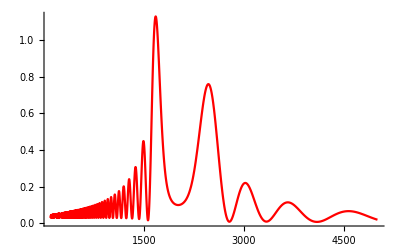

{1.02455,1.03266,1.04046,1.04793,1.05507,1.06188,1.06835,1.0745,1.08031,1.0858,1.09094,1.09576,1.10025,1.1044,1.10823,1.11173,1.1149,1.11775,1.12028,1.12249,1.12438,1.12595,1.12722,1.12818,1.12883,1.12918,1.12924,1.129,1.12848,1.12766,1.12657,1.12521,1.12357,1.12166,1.1195,1.11707,1.1144,1.11148,1.10831,1.10491,1.10129,1.09743,1.09336,1.08907,1.08458,1.07988,1.07498,1.0699,1.06463,1.05918,1.05355}

{0.747082,0.748053,0.748988,0.749887,0.750748,0.751573,0.75236,0.75311,0.753823,0.754498,0.755135,0.755733,0.756294,0.756816,0.7573,0.757744,0.75815,0.758517,0.758845,0.759133,0.759383,0.759592,0.759762,0.759892,0.759983,0.760033,0.760044,0.760014,0.759945,0.759835,0.759684,0.759494,0.759263,0.758991,0.758679,0.758326,0.757933,0.7575,0.757025,0.756511,0.755955,0.755359,0.754722,0.754045,0.753327,0.752569,0.75177,0.750931,0.750051,0.749131,0.748171}

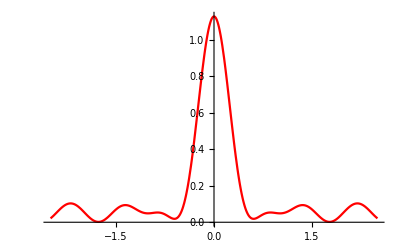

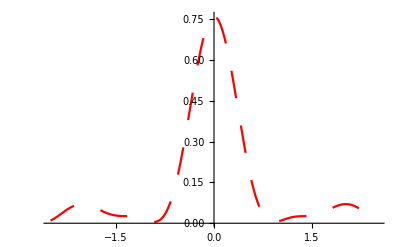

```mathematica
(* Laue symetrique *)
asym=t*Sin[teta]; sym=k*Sqrt[chih2]/Sin[2*teta];{"Za",sym*asym}
attsym=Exp[-k*Im[chizero]*t/Cos[teta]];{"attsym",attsym}
psisym[x_,q_]:=2*NIntegrate[BesselJ[0,sym*Sqrt[(asym+v)*(asym-v)]]*Exp[I*k*0.5*v^2*(raygam-q)/(q*raygam)]*Cos[k*v*x/q],{v,0,asym}];
intsym=Plot[attsym*Abs[psisym[0,q]^2/(lambda*(p+q))],{q,100,5000},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[1,0,0]}] 
ps1=Table[attsym*Abs[psisym[0,q]^2/(lambda*q)],{q,1650,1700,1}] 
ps2=Table[attsym*Abs[psisym[0,q]^2/(lambda*q)],{q,2440,2490,1}]  
focsym1=Plot[attsym*Abs[psisym[xprim*0.001,1675]^2/(lambda*(p+1675))],{xprim,-2.5,2.5},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[1,0,0]}]
focsym2=Plot[attsym*Abs[psisym[xprim*0.001,2466]^2/(lambda*(p+2466))],{xprim,-2.5,2.5},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[1,0,0],Dashing[{0.05,0.05}]}]
```

{qpoly,0.}

0.988279

{u2max,66.7258-0.0337308 ⅈ}

{gama,0.999957}

{a,0.024714}

{kin,-6.57984×10^-11+1.26924×10^-14 ⅈ}

{kiny,1.26924×10^-14}

{com,0.00193675}

{kp3,123799.}

{mu1,1.03949}

{mu2,-0.961118}

{acmax,-4.85414}

{g,-0.0392064}

{kap,-13.7462+0.00694887 ⅈ}

{pe,0.}

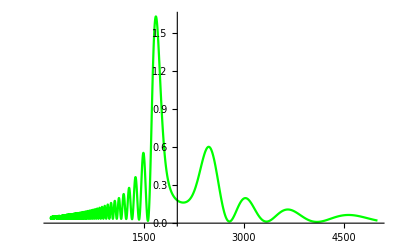

{0.489302,0.509888,0.530689,0.551685,0.572859,0.594193,0.615667,0.637264,0.658965,0.680751,0.702606,0.724509,0.746444,0.768393,0.790338,0.812261,0.834145,0.855973,0.877728,0.899394,0.920954,0.942392,0.963692,0.98484,1.00582,1.02662,1.04721,1.0676,1.08776,1.10769,1.12736,1.14677,1.1659,1.18474,1.20328,1.22152,1.23943,1.25701,1.27425,1.29114,1.30767,1.32384,1.33963,1.35504,1.37006,1.38468,1.3989,1.41271,1.42611,1.4391,1.45166,1.46379,1.47549,1.48676,1.4976,1.508,1.51795,1.52747,1.53654,1.54517,1.55335,1.56109,1.56839,1.57525,1.58166,1.58763,1.59316,1.59826,1.60292,1.60715,1.61095,1.61433,1.61728,1.61982,1.62194,1.62365,1.62495,1.62586,1.62636,1.62648,1.62621,1.62556,1.62454,1.62314,1.62139,1.61928,1.61682,1.61401,1.61087,1.6074,1.6036,1.59949,1.59507,1.59034,1.58532,1.58002,1.57443,1.56857,1.56244,1.55605,1.54942,1.54253,1.53542,1.52807,1.5205,1.51272,1.50473,1.49654,1.48816,1.47959,1.47085,1.46193,1.45286,1.44362,1.43424,1.42472,1.41506,1.40528,1.39537,1.38535,1.37522,1.36499,1.35467,1.34425,1.33376,1.32319,1.31255,1.30184,1.29108,1.28026,1.2694,1.2585,1.24756,1.23659,1.22559,1.21457,1.20354,1.1925,1.18145,1.1704,1.15936,1.14832,1.13729,1.12628,1.11529,1.10433,1.09339,1.08248,1.0716,1.06077,1.04997,1.03922,1.02852,1.01787,1.00727,0.996729,0.986245,0.975822,0.965463,0.955169,0.944944,0.934788,0.924705,0.914695,0.904762,0.894905,0.885128,0.875431,0.865816,0.856285,0.846837,0.837476,0.828201,0.819013,0.809915,0.800905,0.791986,0.783158,0.774421,0.765776,0.757224,0.748764,0.740398,0.732125,0.723946,0.715861,0.70787,0.699972,0.692169,0.68446,0.676845,0.669323,0.661895,0.654561,0.647319,0.64017,0.633113,0.626149,0.619276,0.612494,0.605802}

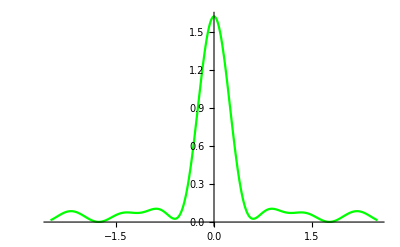

```mathematica
alfa=0.05*Pi/180;teta1=alfa+teta;teta2=alfa-teta;
fam1=Sin[teta1];fam2=Sin[teta2];
gam1=Cos[teta1];gam2=Cos[teta2];t1=t/gam1;t2=t/gam2;
qpoly=p*rayon*gam2/(2*p+rayon*gam1);{"qpoly",qpoly}
att=Exp[-k*0.5*(t1+t2)*Im[chizero]]
s2max=0.25*t1*t2;u2max=u2*s2max;{"u2max",u2max}
gama=t2/t1;{"gama",gama}
a=Sin[2*teta]*t1*0.5;{"a",a};{"a",a}
kin=0.25*(t1-t2)*chizero/a;{"kin",kin}
kinx=Re[kin];kiny=Im[kin];{"kiny",kiny}
com=Sin[alfa]*(1+gam1*gam2*(1+rau));{"com",com}
kp3=0.5*k*(gama*a)^2;{"kp3",kp3}
mu1=(Cos[alfa]*2*fam1*gam1+Sin[alfa]*(fam1^2+rau*gam1^2))/(Sin[2*teta]*Cos[teta]);{"mu1",mu1}
mu2=(Cos[alfa]*2*fam2*gam2+Sin[alfa]*(fam2^2+rau*gam2^2))/(Sin[2*teta]*Cos[teta]);{"mu2",mu2}
a1=(0.5*t/Cos[teta])*(Cos[alfa]*Sin[teta1]+rau*Sin[alfa]*Cos[teta1]);
a2=(0.5*t/Cos[teta])*(Cos[alfa]*Sin[teta2]+rau*Sin[alfa]*Cos[teta2]);
acrist=-h*Sin[alfa]*(1+gam1*gam2*(1+rau))/rayon;acmax=acrist*s2max;{"acmax",acmax}
g=gama*acrist*rayon/kp2;{"g",g}
kap=u2max/acmax;{"kap",kap}
pe=p*rayon/(gama^2*(rayon-p*mu2)-g*p);{"pe",pe}
qe[q_]:=q*rayon/(rayon-q*(mu1+g));
be[q_]:=1/qe[q]+1/pe;
le[q_]:=(pe+qe[q])/(1+g*(pe*qe[q]));
invle[q_]:=1/q-mu1/rayon;
sgplus[x_,q_]:=2*NIntegrate[Hypergeometric1F1[I*kap,1,I*acmax*(1-(v/a)^2)]*Exp[0.5*I*k*v^2*invle[q]]*Cos[k*v*(x/q-I*kiny)],{v,0,a}];  
intplus=Plot[Abs[sgplus[0,q]^2*att/(lambda*q)],{q,100,5000},AxesOrigin->{2000,0},PlotRange->All,PlotStyle->{RGBColor[0,1,0]}]     
psplus=Table[Abs[sgplus[0,q]^2*att/(lambda*q)],{q,1600,1800,1}] 
focplus=Plot[Abs[sgplus[xprim*0.001,1679]^2*att/(lambda*1679)],{xprim,-2.5,2.5},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[0,1,0]}]
```

{qpoly,0.}

0.988279

{u2max,66.7258-0.0337308 ⅈ}

{gama,1.00004}

{a,0.024713}

{kin,6.58013×10^-11-1.2693×10^-14 ⅈ}

{kiny,-1.2693×10^-14}

{com,-0.00193675}

{kp3,123810.}

{mu1,0.961118}

{mu2,-1.03949}

{acmax,4.85414}

{g,0.0392097}

{kap,13.7462-0.00694887 ⅈ}

{pe,0.}

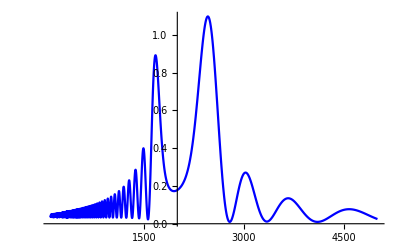

{1.01643,1.01907,1.02167,1.02424,1.02677,1.02926,1.03171,1.03413,1.03651,1.03885,1.04115,1.04341,1.04563,1.04781,1.04995,1.05205,1.0541,1.05612,1.05809,1.06002,1.0619,1.06374,1.06554,1.06729,1.069,1.07066,1.07228,1.07385,1.07538,1.07686,1.07829,1.07968,1.08101,1.0823,1.08355,1.08474,1.08589,1.08698,1.08803,1.08903,1.08997,1.09087,1.09172,1.09252,1.09326,1.09396,1.0946,1.0952,1.09574,1.09623,1.09667,1.09705,1.09738,1.09766,1.09789,1.09807,1.09819,1.09826,1.09827,1.09824,1.09815,1.098,1.0978,1.09755,1.09724,1.09688,1.09647,1.096,1.09548,1.0949,1.09427,1.09358,1.09284,1.09205,1.0912,1.09029,1.08934,1.08832,1.08726,1.08614,1.08496,1.08373,1.08245,1.08111,1.07972,1.07827,1.07677,1.07522,1.07361,1.07195,1.07023,1.06846,1.06664,1.06477,1.06284,1.06086,1.05883,1.05674,1.0546,1.05241,1.05017,1.04788,1.04553,1.04313,1.04068,1.03819,1.03564,1.03304,1.03039,1.02769,1.02494,1.02214,1.01929,1.01639,1.01345,1.01045,1.00741,1.00432,1.00118,0.998001,0.994771,0.991495,0.988172,0.984805,0.981392,0.977934,0.974432,0.970885,0.967295,0.963662,0.959986,0.956267,0.952507,0.948704,0.944861,0.940976,0.937051,0.933087,0.929082,0.925039,0.920957,0.916837,0.91268,0.908485,0.904253,0.899985,0.895682,0.891343,0.886969,0.882562,0.87812,0.873645,0.869137,0.864598,0.860026,0.855423,0.85079,0.846126,0.841433,0.836711,0.83196,0.827181,0.822375,0.817542,0.812683,0.807798,0.802887,0.797953,0.792994,0.788011,0.783006,0.777978,0.772928,0.767858,0.762766,0.757655,0.752524,0.747374,0.742206,0.73702,0.731817,0.726598,0.721363,0.716112,0.710847,0.705567,0.700274,0.694968,0.68965,0.68432,0.678979,0.673627,0.668265,0.662894,0.657514,0.652126,0.646731,0.641329,0.63592,0.630505,0.625086}

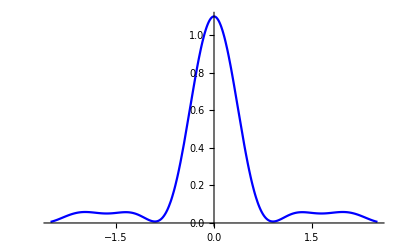

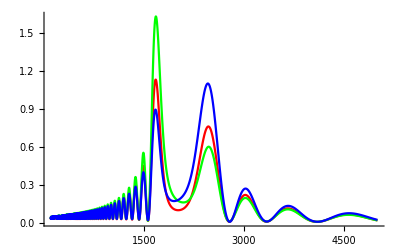

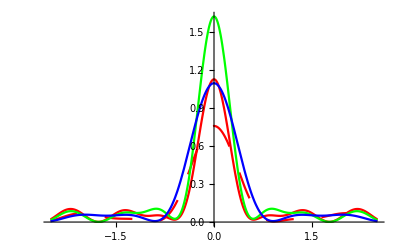

```mathematica
alfa=-0.05*Pi/180;teta1=alfa+teta;teta2=alfa-teta;
fam1=Sin[teta1];fam2=Sin[teta2];
gam1=Cos[teta1];gam2=Cos[teta2];t1=t/gam1;t2=t/gam2;
qpoly=p*rayon*gam2/(2*p+rayon*gam1);{"qpoly",qpoly}
att=Exp[-k*0.5*(t1+t2)*Im[chizero]]
s2max=0.25*t1*t2;u2max=u2*s2max;{"u2max",u2max}
gama=t2/t1;{"gama",gama}
a=Sin[2*teta]*t1*0.5;{"a",a};{"a",a}
kin=0.25*(t1-t2)*chizero/a;{"kin",kin}
kinx=Re[kin];kiny=Im[kin];{"kiny",kiny}
com=Sin[alfa]*(1+gam1*gam2*(1+rau));{"com",com}
kp3=0.5*k*(gama*a)^2;{"kp3",kp3}
mu1=(Cos[alfa]*2*fam1*gam1+Sin[alfa]*(fam1^2+rau*gam1^2))/(Sin[2*teta]*Cos[teta]);{"mu1",mu1}
mu2=(Cos[alfa]*2*fam2*gam2+Sin[alfa]*(fam2^2+rau*gam2^2))/(Sin[2*teta]*Cos[teta]);{"mu2",mu2}
a1=(t/Cos[teta])*(Cos[alfa]*Sin[teta1]+rau*Sin[alfa]*Cos[teta1]);
a2=(t/Cos[teta])*(Cos[alfa]*Sin[teta2]+rau*Sin[alfa]*Cos[teta2]);
acrist=-h*Sin[alfa]*(1+gam1*gam2*(1+rau))/rayon;acmax=acrist*s2max;{"acmax",acmax}
g=gama*acrist*rayon/kp2;{"g",g}
kap=u2max/acmax;{"kap",kap}
pe=p*rayon/(gama^2*(rayon-p*mu2)-g*p);{"pe",pe}
qe[q_]:=q*rayon/(rayon-q*(mu1+g));
be[q_]:=1/qe[q]+1/pe;
le[q_]:=(pe+qe[q])/(1+g*(pe*qe[q]));
invle[q_]:=1/q-mu1/rayon;
sgmoins[x_,q_]:=2*NIntegrate[Hypergeometric1F1[I*kap,1,I*acmax*(1-(v/a)^2)]*Exp[0.5*I*k*v^2*invle[q]]*Cos[k*v*(x/q-I*kiny)],{v,0,a}];  
intmoins=Plot[Abs[sgmoins[0,q]^2*att/(lambda*q)],{q,100,5000},AxesOrigin->{2000,0},PlotRange->All,PlotStyle->{RGBColor[0,0,1]}]     
psmoins=Table[Abs[sgmoins[0,q]^2*att/(lambda*q)],{q,2400,2600,1}] 
focmoins=Plot[Abs[sgmoins[xprim*0.001,2458]^2*att/(lambda*2458)],{xprim,-2.5,2.5},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[0,0,1]}] 


Show[intsym,intplus,intmoins] 
Show[focsym1,focsym2,focplus,focmoins]
```